```mathematica
Clear[predPrMonFNRTheor]; 

(* copying here *) 
predPrMonFNRTheor[detFPR_, monWin_, pDetNCH0_:0(* for this context *)] := 1 - (1-detFPR)(1 - detFPR - pDetNCH0)^(monWin-1);
```

```mathematica
(* detector FPR/FNR estimates for NCC *) 
N@predFPRfromData[fullStatefulTripleList[{4,5,6,7}, #], detFilenames]&/@ stWeightsDetAndPr
```

{0.115307,0.117316,0.125753,0.140217,0.139815,0.166332,0.167135,0.185617,0.171957,0.20691}

```mathematica
N@predFNRfromData[fullStatefulTripleList[{4,5,6,7}, #], detFilenames]&/@ stWeightsDetAndPr
```

{0.10305,0.111555,0.113533,0.122315,0.128486,0.133075,0.143953,0.155505,0.160252,0.165829}

```mathematica
(* Bad ECC: our monitor FNR prediction based on the old FPR of 0.1*) 
N@predPrMonFNRTheor[0.1, 10]
```

0.651322

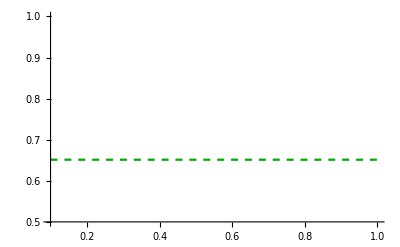

```mathematica
badStatefulECCChart = chartHorLine[predPrMonFNRTheor[0.1, 10],(*max-X*)1.8,0.1,Darker@Green, {Dashed},PlotRange->{{0.1,1},{0.5,1}}]
```

```mathematica
(* NCC: our monitor FNR prediction based on the new FPR *) 
N@predPrMonFNRTheor[predFPRfromData[fullStatefulTripleList[{4,5,6,7}, #], detFilenames], 10]&/@ stWeightsDetAndPr
```

{0.706286,0.712888,0.739181,0.779256,0.778222,0.837844,0.839401,0.871682,0.848459,0.901548}

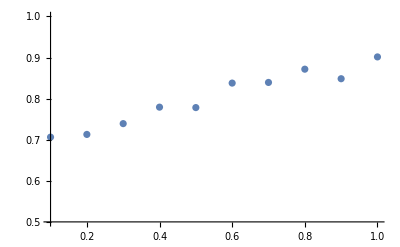

```mathematica
predStatefulFNRChart= ListPlot[Inner[List,  Range[0.1,1,0.1],predPrMonFNRTheor[predFPRfromData[fullStatefulTripleList[{4,5,6,7}, #], detFilenames], 10]&/@ stWeightsDetAndPr, List],PlotStyle->{ColorData[97,"ColorList"][[1]], Thickness[0.002]}, PlotRange->{{0.1,1},{0.5,1}}]
```

```mathematica
(* BBC: data-driven estimates of the FNR *)
```

```mathematica
(getMonValues[dataDirPathForSeshNumPostCorr[All], "FNR",#] & /@ stWeightsDetAndPr )// Flatten[#,1]&
```

{0.696893,0.684211,0.7026,0.700063,0.695625,0.718453,0.714014,0.772987,0.686113,0.715282}

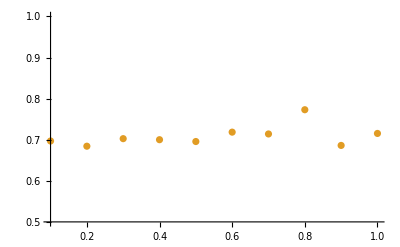

```mathematica
estStatefulFNRChart= ListPlot[Inner[List, Range[0.1,1,0.1],getMonValues[dataDirPathForSeshNumPostCorr[All], "FNR",#] & /@ stWeightsDetAndPr // Flatten[#,1]&, List],PlotStyle->{ColorData[97,"ColorList"][[2]], Thickness[0.002]}, PlotRange->{{0.1,1},{0.5,1}}]
```

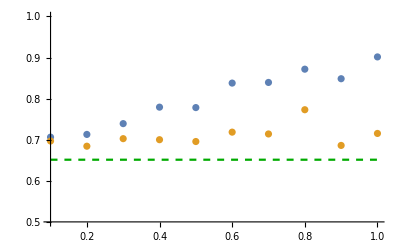

```mathematica
(* combination *) 
Show[badStatefulECCChart, predStatefulFNRChart, estStatefulFNRChart(*PlotRange->{{0.1,1},{0,1}}*)]
```

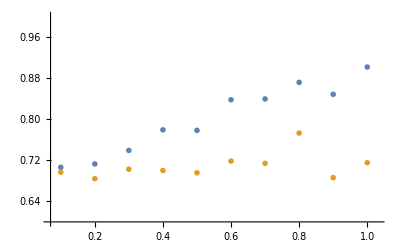

```mathematica
(* production figures *) 

prodPrPlotNCCBBC = ListPlot[{Inner[List,  Range[0.1,1,0.1],predPrMonFNRTheor[predFPRfromData[fullStatefulTripleList[{4,5,6,7}, #], detFilenames], 10]&/@ stWeightsDetAndPr, List], Inner[List, Range[0.1,1,0.1],getMonValues[dataDirPathForSeshNumPostCorr[All], "FNR",#] & /@ stWeightsDetAndPr // Flatten[#,1]&, List]}, PlotRange->{{0.07,1.03},{0.6,1}}, PlotMarkers->{Magnify[openMarkers[[1]], 5], Magnify[openMarkers[[2]],5]}]
```

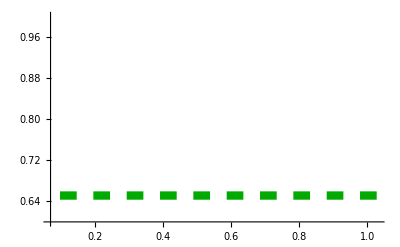

```mathematica
prodPrPlotNCC = chartHorLine[predPrMonFNRTheor[0.1, 10],(*max-X magic*)1.9,0,Darker@Green, {AbsoluteThickness[6],AbsoluteDashing[12]},PlotRange->{{0.07,1.03},{0.6,1}}]
```

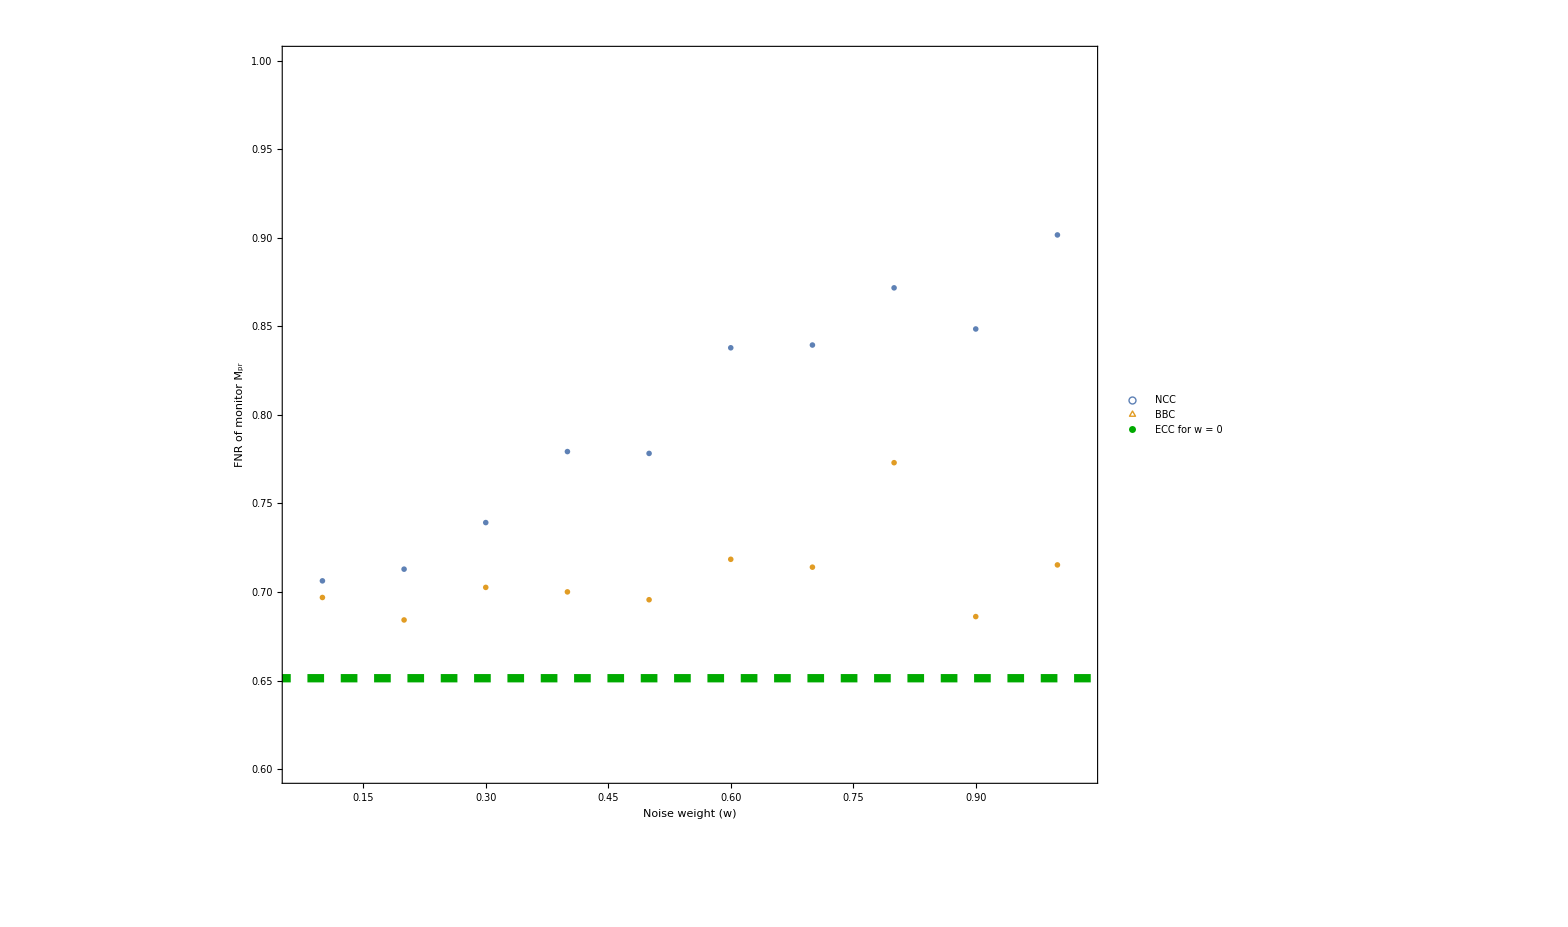

```mathematica
Legended[Show[prodPrPlotNCCBBC, prodPrPlotNCC, Frame->True, FrameLabel->{StringJoin["Noise weight ", ToString[ Style["(w)", Italic], StandardForm] ],StringJoin["FNR of monitor ", ToString[Style[Subscript[ "M", "pr"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->45}], Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]},  {ColorData[97,"ColorList"][[2]]},{AbsoluteDashing[10],AbsoluteThickness[6],Darker@Green}},{"NCC","BBC",StringJoin["ECC for ",ToString[ Style["w = 0", Italic],StandardForm]] },
LegendMarkerSize->50,LegendMarkers->{Style[○,Bold,FontSize->55] ,Style[△,Bold,FontSize->60], Graphics[{Line[{{-10,0},{10,0}}]}](*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.15,0.8}]]
```